```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-up-xi1.wdx"];
Hdg=Query[1,1]@gpd;
Her=Query[1,2]@gpd;
Hda=Query[1,3]@gpd;
Edg=Query[2,1]@gpd;
Eer=Query[2,2]@gpd;
Eda=Query[2,3]@gpd;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

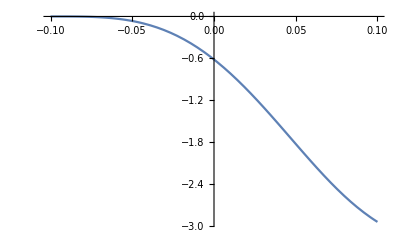

```mathematica
Plot[I*Herf[x,-1],{x,-0.1,0.1}]
```

```mathematica
Plot3D[Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0696428,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0705357,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0700893,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[Plot3D[Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0696428,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0705357,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0700893,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[Plot3D[Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

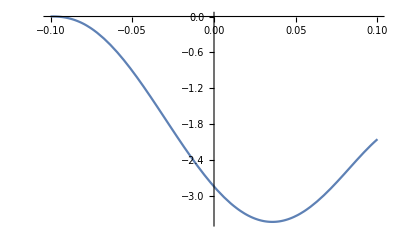

```mathematica
Plot[-I*Chop[Eerf[x,-0.1],10^-9],{x,-0.1,0.1}]
```

```mathematica
Eerf[0,-0.1]
```

0.-2.83547 ⅈ

```mathematica
Eerf[0.02,-0.1]
```

-8.32662×10^-26-3.30567 ⅈ

```mathematica
Eerf[-0.005,-0.1]
```

-1.49999×10^-11-2.67216 ⅈ

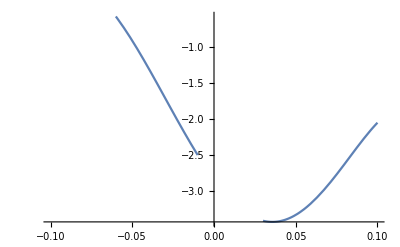

```mathematica
Plot[-I*Eerf[x,-0.1],{x,-0.1,0.1}]
```

```mathematica
Plot3D[I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-